```mathematica
Group Members: Guy F. Mongelli , Daoning Zhou, Gerardo Ortaga, ZhiChao Yao 
Prof. R.M. Sankaran                                                                              EChE 462;            4/24/2013;
```

```mathematica
Final Group Assignment;
```

```mathematica
Problem #1;
```

```mathematica
τ=10 (*s *);
```

```mathematica
k=1 (* 1/s*);
```

```mathematica
let the dimensionless concentration be defined as psi=c/c0;
```

Set::write: Tag Times in as\ be\ concentration\ defined\ dimensionless\ let\ psi\ the is Protected.

c/c0

```mathematica
psi[t_]=(t/τ)Exp[-t/τ];
```

```mathematica
To see how the system will or will not normalize, compute:
```

```mathematica
∫_0^∞ psi[t]ⅆt
```

10

```mathematica
The time at which the concentration exiting the reactor is less than .001 is 91 seconds.  This plot goes to 100 seconds;
```

```mathematica
Solve[psi[t]==.001,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→0.01001}}

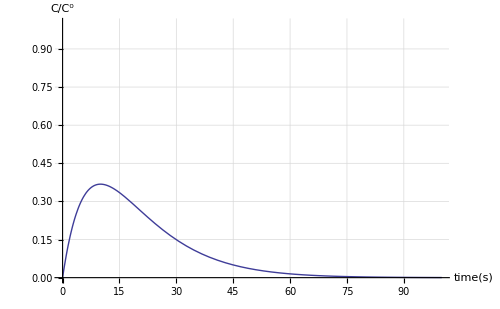

```mathematica
Plot[psi[t],{t,0,100},AxesLabel->{Style["time(s)",15],Style["C/C^0",15]},PlotRange->{0,1}, ImageSize-> 500, GridLines-> Automatic]
```

```mathematica
To normailze this dimensionless concentration, divide by ten.
```

```mathematica
denom=∫_0^∞ psi[t]ⅆt
```

10

```mathematica
Problem 2:
```

```mathematica
Then define the exit time as Ex(t) as:
```

```mathematica
Ex[t_]=psi[t]/(∫_0^∞ psi[t]ⅆt)
```

1/100 ⅇ^(-t/10) t

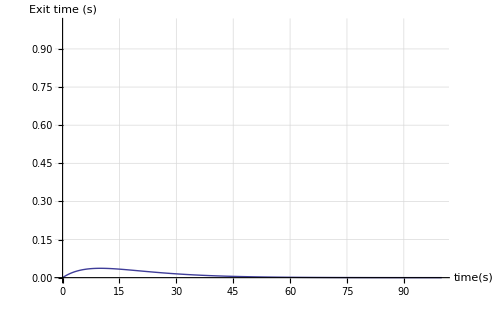

```mathematica
Plot[Ex[t],{t,0,100},AxesLabel->{Style["time(s)",15],Style["Exit time (s)",15]},PlotRange->{0,1}, ImageSize-> 500, GridLines-> Automatic]
```

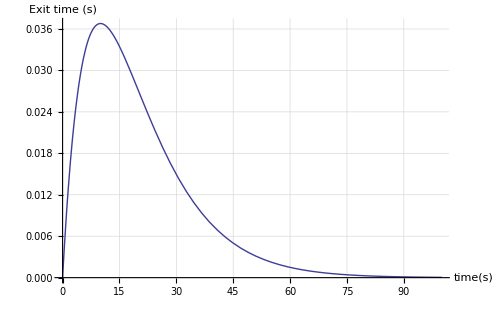

```mathematica
Plot[Ex[t],{t,0,100},AxesLabel->{"time(s)","Exit time (s)"}, ImageSize-> 500, GridLines-> Automatic]
```

```mathematica
Problem 3:
```

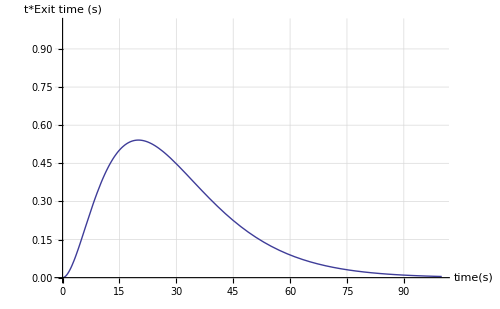

```mathematica
Plot[t*Ex[t],{t,0,100},AxesLabel->{Style["time(s)",15],Style["t*Exit time (s)",15]},PlotRange->{0,1}, ImageSize-> 500, GridLines-> Automatic]
```

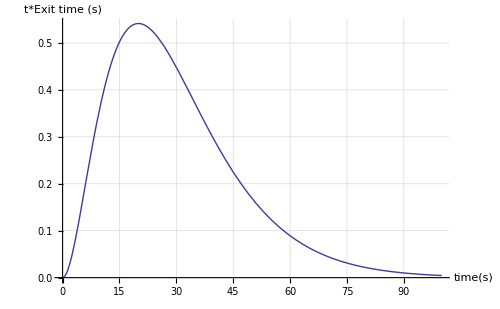

```mathematica
Plot[t*Ex[t],{t,0,100},AxesLabel->{Style["time(s)",15],Style["t*Exit time (s)",15]}, ImageSize-> 500, GridLines-> Automatic]
```

```mathematica
The average residence time (s) comes from the integral definition:
```

```mathematica
AverageTime=(∫_0^100 t*Ex[t]ⅆt)/(∫_0^100 Ex[t]ⅆt)
```

(20 (1-61/ⅇ^10))/(1-11/ⅇ^10)

```mathematica
N[AverageTime]
```

19.9546

```mathematica
The average time is also the time corresponding to the maximum value of t*Ex[t].
```

```mathematica
FindMaximum[t*Ex[t],{t,100}]
```

{0.541341,{t→20.}}

```mathematica
Problem 4:
```

```mathematica
The expectation value for the average concentration is then,cAvg:
```

```mathematica
Cavg should definitely be calculated with the first moment of Exp[-k*t] wrt Ex[t] and not psi[t] wrt Ex[t].
```

```mathematica
cAvg=∫_0^∞ psi[t]*Ex[t]ⅆt
```

1/4

```mathematica
N[1/4]
```

0.25

```mathematica
Problem 5:
```

```mathematica
The ideal CSTR case was derived in class and the results are presented here:
```

```mathematica
psiIdeal[t_]=Exp[-k*t];
```

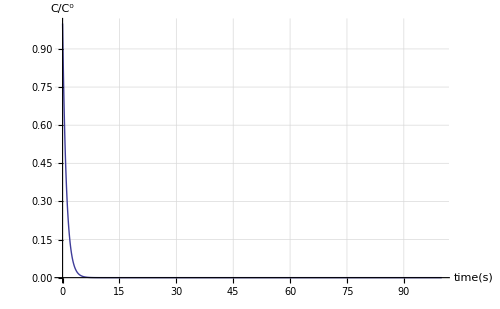

```mathematica
Plot[psiIdeal[t],{t,0,100},AxesLabel->{Style["time(s)",15],Style["C/C^0",15]},PlotRange->{0,1},ImageSize-> 500, GridLines-> Automatic]
```

```mathematica
Plot[psiIdeal[t],{t,0,100},AxesLabel->{Style["time(s)",15],Style["C/C^0",15]},PlotRange->{0,1},ImageSize-> 500, GridLines-> Automatic]
```

-Graphics-

```mathematica
denom2=∫_0^∞ psiIdeal[t]ⅆt
```

1

```mathematica
Then define the exit time as Ex(t) as:
```

```mathematica
Ex2[t_]=psiIdeal[t]/(∫_0^∞ psiIdeal[t]ⅆt)
```

ⅇ^-t

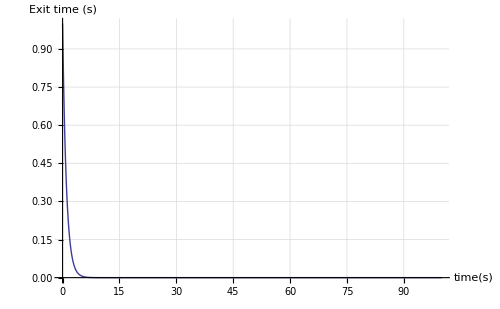

```mathematica
Plot[Ex2[t],{t,0,100},AxesLabel->{Style["time(s)",15],Style["Exit time (s)",15]},PlotRange->{0,1},ImageSize-> 500, GridLines-> Automatic]
```

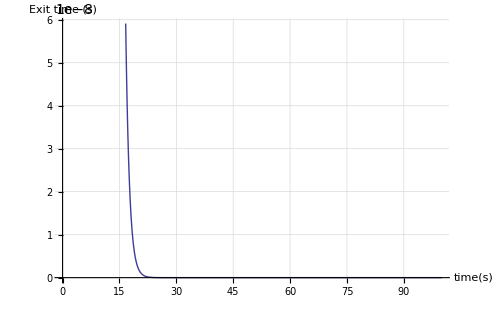

```mathematica
Plot[Ex2[t],{t,0,100},AxesLabel->{Style["time(s)",15],Style["Exit time (s)",15]},ImageSize-> 500, GridLines-> Automatic]
```

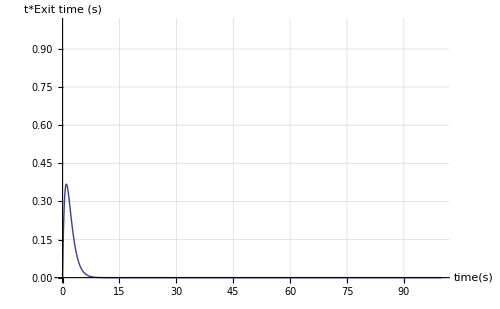

```mathematica
Plot[t*Ex2[t],{t,0,100},AxesLabel->{Style["time(s)",15],Style["t*Exit time (s)",15]},PlotRange->{0,1},ImageSize-> 500, GridLines-> Automatic]
```

```mathematica
Plot[t*Ex2[t],{t,0,100},AxesLabel->{Style["time(s)",15],Style["t*Exit time (s)",15]},PlotRange->{0,1},ImageSize-> 500, GridLines-> Automatic]
```

-Graphics-

```mathematica
The average value comes from the integral definition:
```

```mathematica
AverageTime2=(∫_0^100 t*Ex2[t]ⅆt)/(∫_0^100 Ex2[t]ⅆt)
```

(1-101/ⅇ^100)/(1-1/ⅇ^100)

```mathematica
N[AverageTime2]
```

1.

```mathematica
The expectation value for the average concentration is then,cAvg:
```

```mathematica
cAvg2=∫_0^∞ psiIdeal[t]*Ex2[t]ⅆt
```

1/2

```mathematica
For the ideal case: C[t]=Exp[-k*t]
```

Set::write: Tag Times in For\ ideal\ the\ (case : C[t]) is Protected.

ⅇ^-t

```mathematica
cAvg2=∫_0^∞ Exp[-k*t]*Ex2[t]ⅆt
```

1/2

```mathematica
In the ideal case, the average concentration is higher, which idicates a lower conversion.
```

```mathematica
On the same axes, the figures are:
```

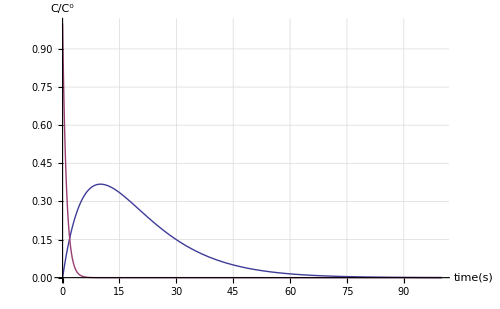

```mathematica
Plot[{psi[t],psiIdeal[t]},{t,0,100},AxesLabel->{Style["time(s)",15],Style["C/C^0",15]},PlotRange->{0,1},ImageSize-> 500, GridLines-> Automatic]
```

```mathematica
Plot[{psi[t],psiIdeal[t]},{t,0,100},PlotRange->{0,1},AxesLabel->{Style["time(s)",15],Style["C/C^0",15]},ImageSize-> 500, GridLines-> Automatic]
```

-Graphics-

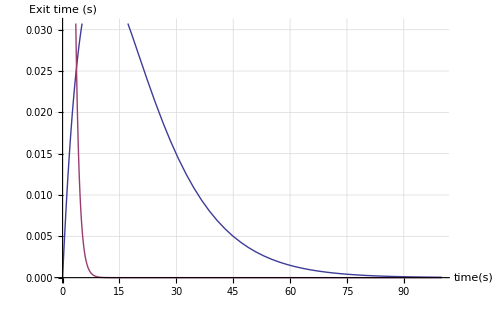

```mathematica
Plot[{Ex[t],Ex2[t]},{t,0,100},AxesLabel->{Style["time(s)",15],Style["Exit time (s)",15]},ImageSize-> 500, GridLines-> Automatic]
```

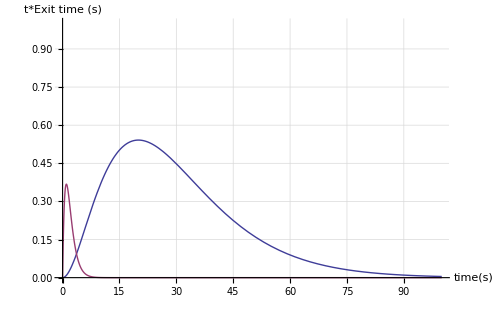

```mathematica
Plot[{t*Ex[t],t*Ex2[t]},{t,0,100},AxesLabel->{Style["time(s)",15],Style["t*Exit time (s)",15]},PlotRange->{0,1},ImageSize-> 500, GridLines-> Automatic]
```

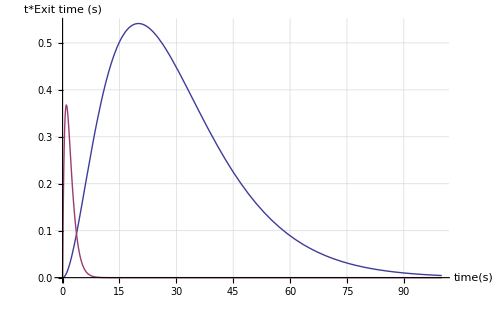

```mathematica
Plot[{t*Ex[t],t*Ex2[t]},{t,0,100},AxesLabel->{Style["time(s)",15],Style["t*Exit time (s)",15]},ImageSize-> 500, GridLines-> Automatic]
```

```mathematica
psiIdeal[100]
```

1/ⅇ^100

```mathematica
N[psiIdeal[100],3]
```

3.72×10^-44

```mathematica
psi[100]
```

10/ⅇ^10

```mathematica
N[psi[100],3]
```

0.000454

```mathematica
The expected outlet concentration for an Ideal PFR would be:
```

```mathematica
cAvgPFR=∫_0^∞ psi[t]*DiracDelta[t-τ]ⅆt
```

1/ⅇ

```mathematica
cAvgPFR=∫_0^∞ psiIdeal[t]*DiracDelta[t-τ]ⅆt
```

1/ⅇ^10

```mathematica
psiPFR[t_]=Exp[-k*t];
```

```mathematica
cAvgPFR=∫_0^∞ psiPFR[t]*DiracDelta[t-τ]ⅆt
```

1/ⅇ^10